```mathematica
Id = {{1,0},{0,1}};
X={{0,1},{1,0}};
Y={{0,-ⅈ},{ⅈ,0}};
Z={{1,0},{0,-1}};
H = a (KroneckerProduct[X,X,Id,Id,Id]+KroneckerProduct[Id,X,X,Id,Id]+KroneckerProduct[Id,Id,X,X,Id]+KroneckerProduct[Id,Id,X,Id,X])+b (KroneckerProduct[Y,Y,Id,Id,Id]+KroneckerProduct[Id,Y,Y,Id,Id]+KroneckerProduct[Id,Id,Y,Y,Id]+KroneckerProduct[Id,Id,Y,Id,Y])+
c (KroneckerProduct[Z,Z,Id,Id,Id]+KroneckerProduct[Id,Z,Z,Id,Id]+KroneckerProduct[Id,Id,Z,Z,Id]+KroneckerProduct[Id,Id,Z,Id,Z]);
bitstrings=Tuples[{0,1},5];
evenParity=Select[bitstrings,EvenQ[Total[#]]&];
idx=Flatten[Position[bitstrings,#]&/@evenParity];
Hsub=H[[idx,idx]]/.{a->2,c->-1};
```

```mathematica
{evals,evecs}=Eigensystem[Hsub];
```

```mathematica
evals[[5]]
```

Root[589824-1474560 b^2+3313664 b^4-368640 b^6+36864 b^8+(-3276800 b-3440640 b^3-1376256 b^5-163840 b^7) #1+(-1392640-2035712 b^2-102400 b^4-135168 b^6-20480 b^8) #1^2+(2109440 b+1867776 b^3+327680 b^5+12288 b^7) #1^3+(744448+632320 b^2+157696 b^4+28160 b^6+1024 b^8) #1^4+(-352768 b-168960 b^3-12800 b^5) #1^5+(-111680-74048 b^2-14400 b^4-832 b^6) #1^6+(16640 b+3328 b^3) #1^7+(6256+2720 b^2+240 b^4) #1^8-224 b #1^9+(-140-28 b^2) #1^10+#1^12&,1]

```mathematica
deg12Poly=589824-1474560 b^2+3313664 b^4-368640 b^6+36864 b^8+(-3276800 b-3440640 b^3-1376256 b^5-163840 b^7) λ+(-1392640-2035712 b^2-102400 b^4-135168 b^6-20480 b^8) λ^2+(2109440 b+1867776 b^3+327680 b^5+12288 b^7)λ^3+(744448+632320 b^2+157696 b^4+28160 b^6+1024 b^8) λ^4+(-352768 b-168960 b^3-12800 b^5) λ^5+(-111680-74048 b^2-14400 b^4-832 b^6) λ^6+(16640 b+3328 b^3) λ^7+(6256+2720 b^2+240 b^4) λ^8-224 b λ^9+(-140-28 b^2) λ^10+λ^12;
```

```mathematica
idx=5; (*first idx corresponding to root of degree 12 polynomial*)
evals[[idx]]
root=First@Cases[evecs[[idx]],_Root,∞];
rVec=FullSimplify[evecs[[idx]]/. root->λ];
```

Root[589824-1474560 b^2+3313664 b^4-368640 b^6+36864 b^8+(-3276800 b-3440640 b^3-1376256 b^5-163840 b^7) #1+(-1392640-2035712 b^2-102400 b^4-135168 b^6-20480 b^8) #1^2+(2109440 b+1867776 b^3+327680 b^5+12288 b^7) #1^3+(744448+632320 b^2+157696 b^4+28160 b^6+1024 b^8) #1^4+(-352768 b-168960 b^3-12800 b^5) #1^5+(-111680-74048 b^2-14400 b^4-832 b^6) #1^6+(16640 b+3328 b^3) #1^7+(6256+2720 b^2+240 b^4) #1^8-224 b #1^9+(-140-28 b^2) #1^10+#1^12&,1]

```mathematica
n=5;  
alpha=rVec;
EvenParityBitstrings[n_]:=Select[Tuples[{0,1},n],EvenQ[Total[#]]&];
BitFlip[bs_List,i_Integer]:=ReplacePart[bs,i->1-bs[[i]]];
BitComplement[bs_List]:=1-bs;
B=EvenParityBitstrings[n];
bitToIndex=AssociationThread[B->Range[Length[B]]];
tX=Simplify@Table[Sum[Module[{z=B[[k]],zbar,target,j},zbar=BitComplement[z];
target=BitFlip[zbar,i];(*overline{z}^{(i)}*)j=bitToIndex[target];(*index in B*)alpha[[k]]*alpha[[j]]],{k,Length[B]}],{i,n}];
tY=Simplify@Table[Sum[Module[{z=B[[k]],zbar,target,j},zbar=BitComplement[z];
target=BitFlip[zbar,i];
j=bitToIndex[target];
alpha[[k]]*((-1)^(z[[i]]))*alpha[[j]]],{k,Length[B]}],{i,n}];
tZ=Simplify@Table[Sum[Module[{z=B[[k]]},alpha[[k]]^2*((-1)^(z[[i]]))],{k,Length[B]}],{i,n}];
aEff12=2*tX[[1]]*tX[[2]];
bEff12=b*tY[[1]]*tY[[2]];
cEff12=-1*tZ[[1]]*tZ[[2]];
aEff22=2*tX[[2]]*tX[[2]];
bEff22=b*tY[[2]]*tY[[2]];
cEff22=-1*tZ[[2]]*tZ[[2]];
```

```mathematica
(*Numerical Check*)
{an,bn,cn}={2,-.11,-1};
ln=evals[[idx]]/.{a->an,b->bn,c->cn};
normn=Norm[evecs[[idx]]/.{a->2,b->-.1,c->cn}];
tX1n=tX[[1]]/.{a->an,b->bn,c->cn,λ->ln};
tY1n=tY[[1]]/.{a->an,b->bn,c->cn,λ->ln};
tZ1n=tZ[[1]]/.{a->an,b->bn,c->cn,λ->ln};
tX2n=tX[[2]]/.{a->an,b->bn,c->cn,λ->ln};
tY2n=tY[[2]]/.{a->an,b->bn,c->cn,λ->ln};
tZ2n=tZ[[2]]/.{a->an,b->bn,c->cn,λ->ln};
{tX1n/normn^2,tY1n/normn^2,tZ1n/normn^2,tX2n/normn^2,tY2n/normn^2,tZ2n/normn^2};
aEff12n=aEff12/.{a->an,b->bn,c->cn,λ->ln};
bEff12n=bEff12/.{a->an,b->bn,c->cn,λ->ln};
cEff12n=cEff12/.{a->an,b->bn,c->cn,λ->ln};
aEff22n=aEff22/.{a->an,b->bn,c->cn,λ->ln};
bEff22n=bEff22/.{a->an,b->bn,c->cn,λ->ln};
cEff22n=cEff22/.{a->an,b->bn,c->cn,λ->ln};
```

```mathematica
kn=1/(1-bEff12n/cEff12n cEff22n/bEff22n)
kn aEff12n/(-cEff12n)+(1-kn)aEff22n/(-cEff22n)
kn bEff12n/(-cEff12n)+(1-kn)bEff22n/(-cEff22n)
kn cEff12n/(-cEff12n)+(1-kn)cEff22n/(-cEff22n)
```

0.189736

400.292

2.1684×10^-19

-1.

```mathematica
k=1/(1-bEff12/cEff12 cEff22/bEff22);
aEff = k aEff12/(-cEff12)+(1-k)aEff22/(-cEff22);
```

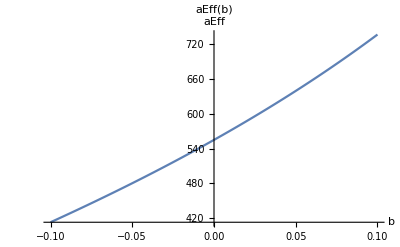

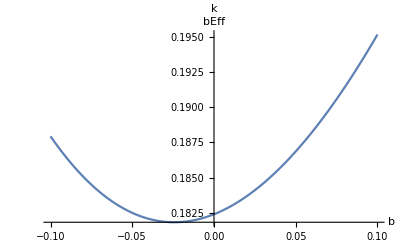

```mathematica
Plot[Module[{ln=evals[[5]]/. b->bb},aEff/. {λ->ln,b->bb}],{bb,-0.1,0.1},PlotRange->All,PlotPoints->100,MaxRecursion->4,AxesLabel->{"b","aEff"},PlotLabel->"aEff(b)"]
Plot[Module[{ln=evals[[5]]/. b->bb},k/. {λ->ln,b->bb}],{bb,-0.1,0.1},PlotRange->All,PlotPoints->100,MaxRecursion->4,AxesLabel->{"b","bEff"},PlotLabel->"k"]
```

```mathematica
(*aEff and derivate*)
(*Step 1:Solve for the smallest real root of deg12Poly at b=0*)λ0=Min[λ/. NSolve[deg12Poly==0/. b->0,λ]];
(*Step 2:Compute dΛ/db at b=0 using implicit differentiation*)
dλdbAt0=-(D[deg12Poly,b]/. {b->0,λ->λ0})/(D[deg12Poly,λ]/. {b->0,λ->λ0});
(*Step 3:Compute daEff/db using the chain rule*)
daEffdbAt0=(D[aEff,b]+D[aEff,λ]*dλdbAt0)/. {b->0,λ->λ0};
(*Optional:numerical value*)
Print["a'(b=0): ", aEff/. {b->0,λ->λ0},"  da'/db(b=0): ",N[daEffdbAt0]]
(*bEff and derivate*)
(*reuse dλ/db from aEff derivative*)
(*Step 3:Compute df/db using the chain rule*)
dkdbAt0=(D[k,b]+D[k,λ]*dλdbAt0)/. {b->0,λ->λ0};
(*Optional:numerical value*)
Print["k(b=0): ", k/. {b->0,λ->λ0},"  db'/db(b=0): ",N[dkdbAt0]]
```

a'(b=0): 555.218  da'/db(b=0): 1584.28

k(b=0): 0.182413  db'/db(b=0): 0.0460397